```mathematica
SetDirectory[NotebookDirectory[]];
```

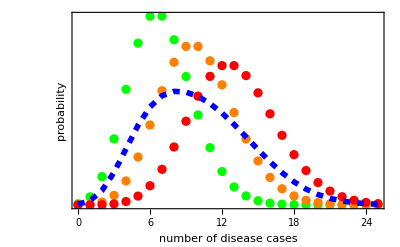

```mathematica
g1=DiscretePlot[{PDF[PoissonDistribution[7],x],PDF[PoissonDistribution[10],x],PDF[PoissonDistribution[13],x],PDF[MixtureDistribution[{1,1,1},{PoissonDistribution[6.5],PoissonDistribution[10],PoissonDistribution[13.5]}],x]},{x,0,25},PlotStyle->{Green,Orange,Red,{Dashed,Blue,Thickness[0.01]}},Joined->{False,False,False,True},Filling->None,Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"number of disease cases","probability"},BaseStyle->Medium]
```

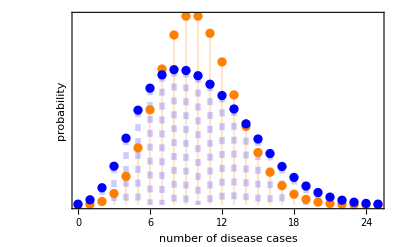

```mathematica
g2=DiscretePlot[{PDF[PoissonDistribution[10],x],PDF[MixtureDistribution[{1,1,1},{PoissonDistribution[6.5],PoissonDistribution[10],PoissonDistribution[13.5]}],x]},{x,0,25},PlotStyle->{Orange,{Dashed,Blue,Thickness[0.01]}},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"number of disease cases","probability"},BaseStyle->Medium]
```

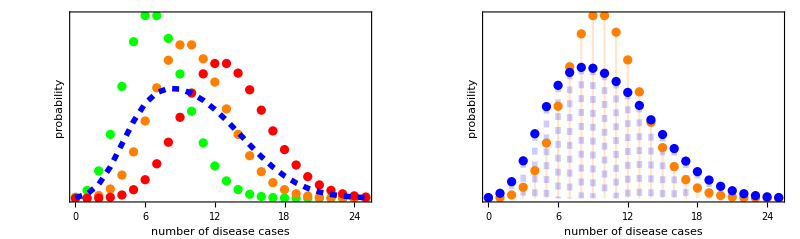

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_negativeBinomialDispersion.pdf",gFinal]
```

Distributions_negativeBinomialDispersion.pdf